## Local decision variable

```mathematica
di[xi_, ks_, kx_] :=(kx * Cos[xi]) + Log[BesselI[0, ks] / (BesselI[0, ((kx^2) + (ks^2) + (2*kx*ks*Cos[xi ]))^0.5])]
```

```mathematica
Information[di]
```

Global`di

di[xi_,ks_,kx_]:=kx Cos[xi]+Log[BesselI[0,ks]/BesselI[0,(kx^2+ks^2+2 kx ks Cos[xi])^0.5]]

## Global decision variable for n=2

```mathematica
d2[x1_, x2_, ks_, kx_] := Log[(1/2) * (Exp[di[x1, ks, kx]] + Exp[di[x2, ks, kx]])]
```

#### Plot for paper

```mathematica
SetOptions[ContourPlot,BaseStyle->{FontSize->10, FontFamily -> "Times New Roman", TicksStyle -> None}]
```

{AlignmentPoint→Center,AspectRatio→1,Axes→False,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{FontSize→10,FontFamily→Times New Roman,TicksStyle→None},BoundaryStyle→None,BoxRatios→Automatic,ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,ContourLabels→Automatic,ContourLines→True,Contours→Automatic,ContourShading→Automatic,ContourStyle→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Evaluated→Automatic,EvaluationMonitor→None,Exclusions→Automatic,ExclusionsStyle→None,FormatType:>TraditionalForm,Frame→True,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelStyle→{},LightingAngle→None,MaxRecursion→Automatic,Mesh→None,MeshFunctions→{},MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLegends→None,PlotPoints→Automatic,PlotRange→{Full,Full,Automatic},PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotateLabel→True,ScalingFunctions→None,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{},WorkingPrecision→MachinePrecision}

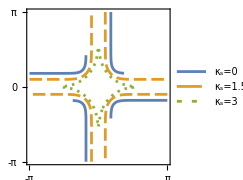

```mathematica
p1 = ContourPlot[{d2[x1, x2, 0, 8]== 0, d2[x1, x2, 1.5, 8]== 0, d2[x1, x2, 3, 8]== 0},{x1,  -Pi, Pi}, {x2, -Pi, Pi},  FrameTicksStyle -> Directive[Black], Frame->{True,True,False,False}, FrameStyle -> Directive[AbsoluteThickness[1]], ContourStyle->{{AbsoluteThickness[2], Dashing[{1}]}, {AbsoluteThickness[2], Dashing[{0.05, 0.02}]}, {AbsoluteThickness[2], Dashing[{0.01, 0.02}]} },FrameTicks->{{{-Pi,0, Pi},None},{{-Pi,0, Pi},None}},  PlotLegends->{"κ_s=0", "κ_s=1.5", "κ_s=3"}, ImageSize -> {180, 180}]
```

```mathematica
Export["decisionThreshold.pdf", p1, ImageResolution -> 300]
```

decisionThreshold.pdf

#### Plot for paper 2

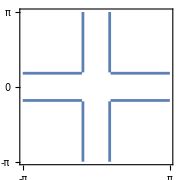

```mathematica
p2 = ContourPlot[{Min[Abs[x1], Abs[x2]] == (Pi/5.5)},{x1,  -Pi, Pi}, {x2, -Pi, Pi},  FrameTicksStyle -> Directive[Black], Frame->{True,True,False,False}, FrameStyle -> Directive[AbsoluteThickness[1]], ContourStyle->{{AbsoluteThickness[2], Dashing[{1}]}, {AbsoluteThickness[2], Dashing[{0.05, 0.02}]}, {AbsoluteThickness[2], Dashing[{0.01, 0.02}]} },FrameTicks->{{{-Pi,0, Pi},None},{{-Pi,0, Pi},None}}, ImageSize -> {180, 180}]
```

```mathematica
Export["decisionThreshold_minRule.pdf", p2, ImageResolution -> 300]
```

decisionThreshold_minRule.pdf